```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.3,Jtwo,0.3,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.5916079783099615}]
```

{z→0.591608}

```mathematica
Clear[IntPlus,NullsHolm,G,P]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.3,l->0.3}
```

0.591608+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
p= Check[FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,p}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.5916079783099615]]
```

{{0.005,0.598404},{0.01,0.605018},{0.015,0.611447},{0.02,0.617686},{0.025,0.623732},{0.03,0.629578},{0.035,0.635218},{0.04,0.640644},{0.045,0.645849},{0.05,0.650822},{0.055,0.655556},{0.06,0.660038},{0.065,0.664258},{0.07,0.668205},{0.075,0.671867},{0.08,0.675233},{0.085,0.67829},{0.09,0.68103},{0.095,0.683443},{0.1,0.685519}}

```mathematica
moduler[Lister[-1,-0.005,0.5916079783099615]]
```

{{-0.005,0.584632},{-0.01,0.577477},{-0.015,0.570145},{-0.02,0.562635},{-0.025,0.554946},{-0.03,0.547076},{-0.035,0.539024},{-0.04,0.530785},{-0.045,0.522356},{-0.05,0.513732},{-0.055,0.504907},{-0.06,0.495873},{-0.065,0.486624},{-0.07,0.477149},{-0.075,0.467437},{-0.08,0.457478},{-0.085,0.447257},{-0.09,0.436758},{-0.095,0.425963},{-0.1,0.414851}}

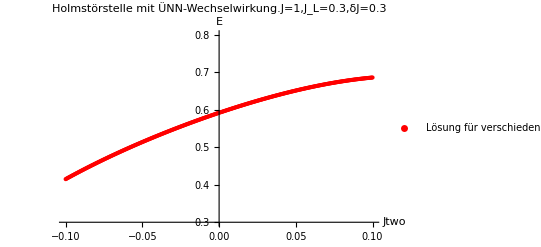

```mathematica
P = ListPlot[Fueger[moduler[Lister[1,0.0005,0.5916079783099615]],moduler[Lister[-1,-0.0005,0.5916079783099615]]],AxesLabel->{Jtwo,"E"},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.3",PlotRange->{0.3,0.8},PlotStyle->Red]
```

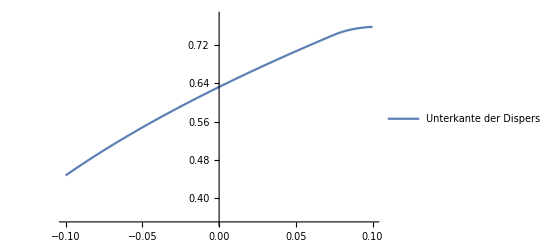

```mathematica
G = Plot[Sqrt[1+2*(0.3*Cos[Inv[0.3,Jtwo]]+Jtwo*Cos[2*Inv[0.3,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.35,0.78},PlotLegends->{"Unterkante der Dispersion"}]
```

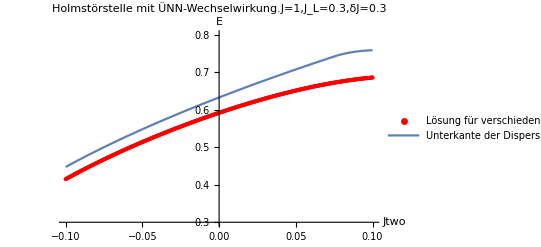

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.3,moduler[Lister[-1,-0.005,0.5916079783099615]]]
```

{{-0.005,0.0398679},{-0.01,0.0389641},{-0.015,0.0381313},{-0.02,0.0373653},{-0.025,0.0366623},{-0.03,0.036019},{-0.035,0.0354325},{-0.04,0.0349002},{-0.045,0.03442},{-0.05,0.0339903},{-0.055,0.0336095},{-0.06,0.0332768},{-0.065,0.0329915},{-0.07,0.0327534},{-0.075,0.0325626},{-0.08,0.0324199},{-0.085,0.0323265},{-0.09,0.032284},{-0.095,0.032295},{-0.1,0.0323625}}

```mathematica
differ[1,0.3,moduler[Lister[1,0.005,0.5916079783099615]]]
```

{{0.005,0.0419083},{0.01,0.043056},{0.015,0.044297},{0.02,0.0456386},{0.025,0.0470885},{0.03,0.0486552},{0.035,0.0503479},{0.04,0.0521764},{0.045,0.0541514},{0.05,0.0562844},{0.055,0.0585871},{0.06,0.0610723},{0.065,0.0637528},{0.07,0.0666418},{0.075,0.651009},{0.08,0.0722633},{0.085,0.0735699},{0.09,0.073953},{0.095,0.0736291},{0.1,0.0727681}}

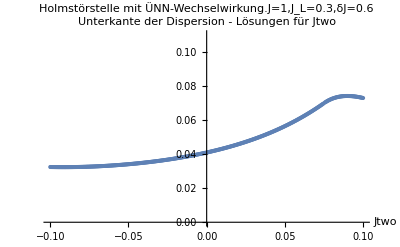

```mathematica
ListPlot[Fueger[differ[-1,0.3,moduler[Lister[-1,-0.0005,0.5916079783099615]]],differ[1,0.3,moduler[Lister[1,0.0005,0.5916079783099615]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.6"]
```